# C & Q Chaos IV - Phenomenology of broken integrability

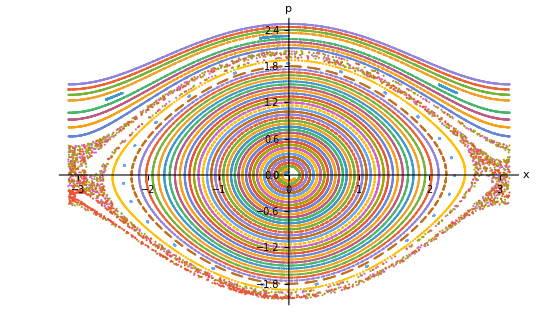
Last time we explored the concept of what is Liouville integrability, and we started discussing what is the route to it being broken. The key element were the homoclinic/heteroclinic orbits and the tangles that they created upon perturbation. This explained the weird phenomenon that we saw around the unstable equilibrium in the phase space of the periodically driven mathematical pendulum. 
-Graphics-

In this lesson, we will wander into similar structures that appear even near resonances. These are parts of the phase space that did not have any unstable equilibria/unstable periodic orbits in the phase space before perturbations.

## Tuning the driving frequency

Consider the unperturbed mathematical pendulum. Near x=0, it is almost a harmonic

```mathematica
Series[ 1/2 p^2 - Cos[x],{x,0,2}]
```

(-1+p^2/2)+x^2/2+O[x]^3

This system has an angular frequency of “1” in the implicit units used here (or ordinary frequency 1/2π). However, the frequency asymptotically reaches zero before reaching the homoclinic orbit. So, the librations have frequencies between 0 and 1. 

Now consider the perturbing term that we used to drive the pendulum

```mathematica
ϵ Cos[x] Sin[τ]
```

ϵ Cos[x] Sin[τ]

This also has the frequency of 1/2π. In other words, we were driving the system at the same frequency as its lowest-energy oscillation. Do we get a generic picture from that? Let’s check.

```mathematica
Hnaτ[p_,x_,pτ_,τ_] :=  1/2 p^2 - Cos[x] +ϵ Cos[x] Sin[τ] + ω pτ;
```

This Hamiltonian will drive the system at frequency ω/2π  since τ’=ω. Let us explore its dynamics

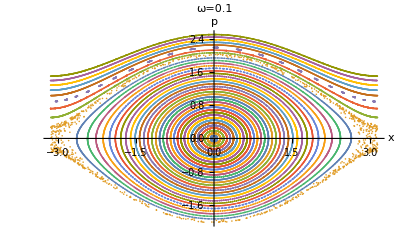
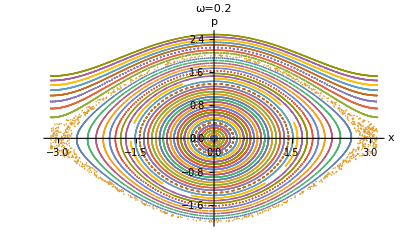
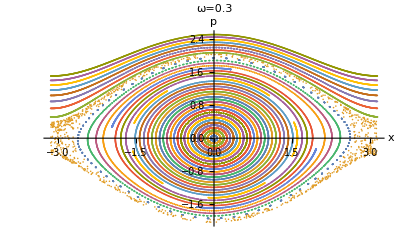
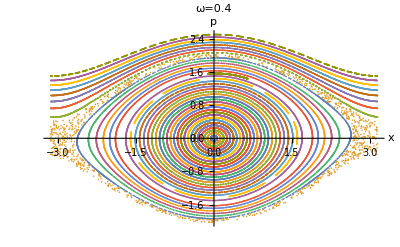
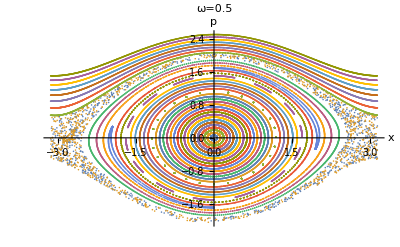
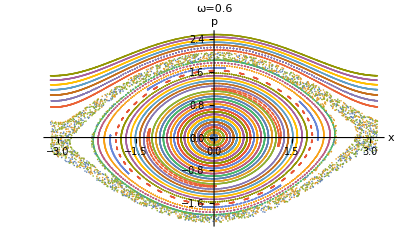
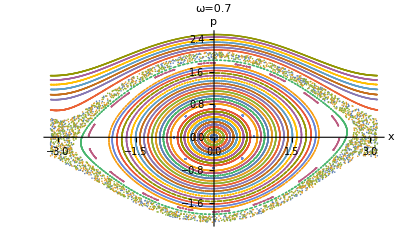
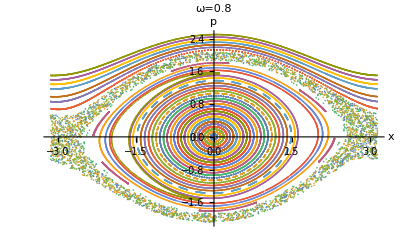

```mathematica
CanCList = {p,x,pτ,τ};

TrajRule = Table[CanCList[[i]]->CanCList[[i]][t] ,{i,1,Length[CanCList]}];

EOM = {p'[t] == (-D[Hnaτ[p,x,pτ,τ],x]/.TrajRule),pτ'[t] == (-D[Hnaτ[p,x,pτ,τ],τ]/.TrajRule),x'[t]==(D[Hnaτ[p,x,pτ,τ],p]/.TrajRule),τ'[t] == (D[Hnaτ[p,x,pτ,τ],pτ]/.TrajRule)};

SnapSet[Init_,n_,ϵ0_,ω0_] := Module[{pxSet},
pxSet = Block[{ϵ=ϵ0,ω=ω0},Reap[NDSolve[Join[EOM,Init,{WhenEvent[Mod[τ[t],2π]==0,Sow[{Mod[x[t]+π,2π]-π,p[t]}]]}],{p,pτ,x,τ},{t,0, 2 π n/ω0},PrecisionGoal->10,AccuracyGoal->10]]];
pxSet[[2,1]]
]

imax=40;
(*We know that for the unperturbed pendulum the separatrix was at E=1. This corresponds to, e.g. x=0 and p=√2. We can than take a look at initial conditions starting from p=0 and going over √2>*)
InitTable = Table[{p[0]==0+2.5 i/imax,pτ[0]==0,τ[0]==0,x[0]==0},{i,1,imax}];

jmax=10;
ωSnaps = Table[Block[{ω=j/jmax},SnapSet[InitTable[[i]],1000,0.1,ω]],{j,1,jmax},{i,1,imax}]
ωTab = Table[ListPlot[ωSnaps[[j]],AxesLabel->{"x","p"},PlotLabel->"ω="<>ToString[Evaluate[N[j/jmax]]]],{j,1,jmax}]
```

What are these new structures? Why do they occur in different parts of phase space for every driving frequency? Does it have something to do with the frequency of the unperturbed system?
 
 Let us take a look.

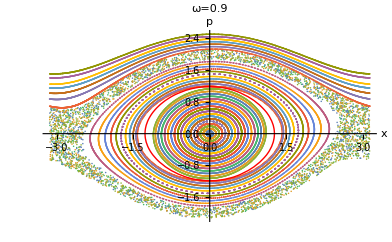

```mathematica
(*Numerically invert for energy as a function of frequency*)
Energy[Ωx_]:=Chop[En/.FindRoot[Ωx ==π/(2 √2 √(1/(1+En)) EllipticF[ArcCos[-En]/2,2/(1+En)]),{En,0}]];
(*Now let us plot the energy contour corresponding to the driving frequency*)
Show[ωTab[[9]],ContourPlot[Energy[0.9]==1/2 p^2 - Cos[x],{x,-π,π},{p,-3,3},ContourStyle->Directive[Red,Thick]]]
```

-> The new structure is connected with resonance. That is, the system responds strongly when the driving and unperturbed frequency are equal. Let us take a closer look at what happens there.

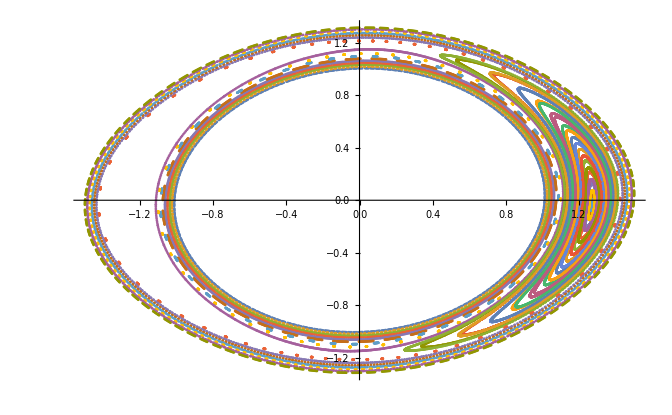

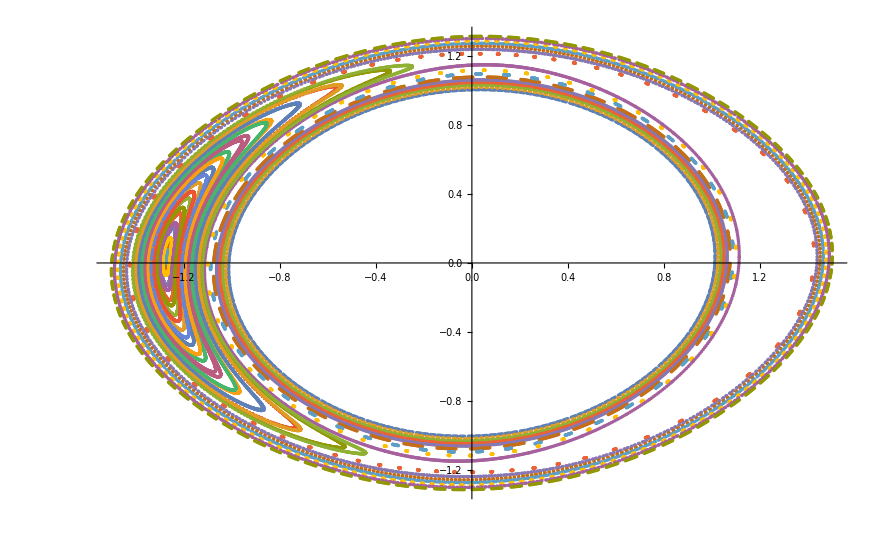

```mathematica
ResoInit1 = Table[{p[0]==0,pτ[0]==0,τ[0]==0,x[0]==1. + 0.5i/imax},{i,1,imax}];
ListPlot[Table[SnapSet[ResoInit1[[i]],1000,0.1,0.9],{i,1,imax}]]
ResoInit2 = Table[{p[0]==0,pτ[0]==0,τ[0]==0,x[0]==-1. - 0.5i/imax},{i,1,imax}];
ListPlot[Table[SnapSet[ResoInit2[[i]],1000,0.1,0.9],{i,1,imax}]]
```

Interesting stuff! The perturbation has created a nonlinear pendulum within the nonlinear pendulum! The motion librates around a periodic orbit (there are two copies of the orbit for x>0 and x<0). There are also unstable periodic orbits along x=0, and roughly p = +-1.2. 

Obviously, the unstable periodic orbits also allow for a homoclinic tangle! Let’s try to take a look.

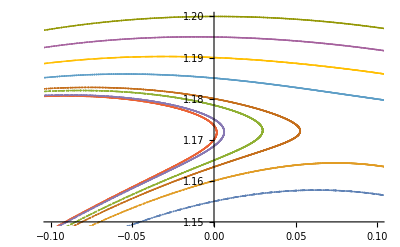

```mathematica
ResoInit3 = Table[{p[0]==1.15+0.05i/10,pτ[0]==0,τ[0]==0,x[0]==0},{i,1,10}];
ListPlot[Table[SnapSet[ResoInit3[[i]],10000,0.1,0.9],{i,1,10}],PlotRange->{{-0.1,0.1},{1.15,1.2}}]
```

The tangle and the chaotic layer can be a very subtle feature but it is likely there.

Now consider this, however. We try to drive the oscillator with a frequency that is higher than any frequency within the system:

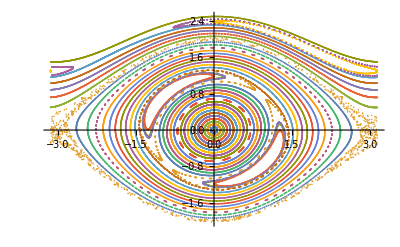

```mathematica
DoubleResoPlot = ListPlot[Table[SnapSet[InitTable[[i]],1000,0.01,1.8],{i,1,imax}]]
```

This is at the same location as the ω=0.9 libration! Note also that the ϵ parameter is ten times smaller.

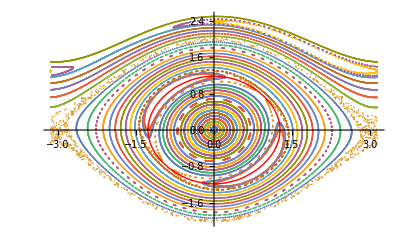

```mathematica
Show[DoubleResoPlot,ContourPlot[Energy[0.9]==1/2 p^2 - Cos[x],{x,-π,π},{p,-3,3},ContourStyle->Directive[Red,Thick]]]
```

Let us play this game even more:

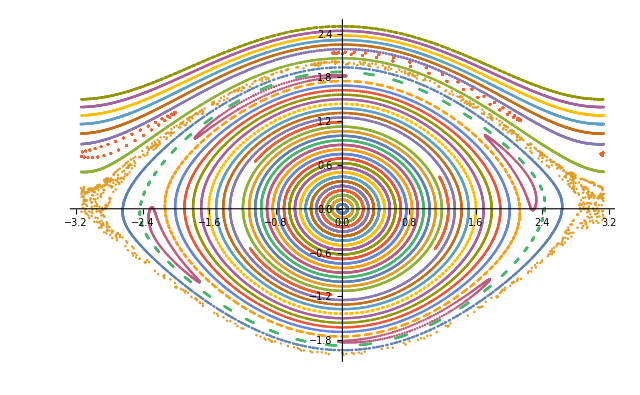

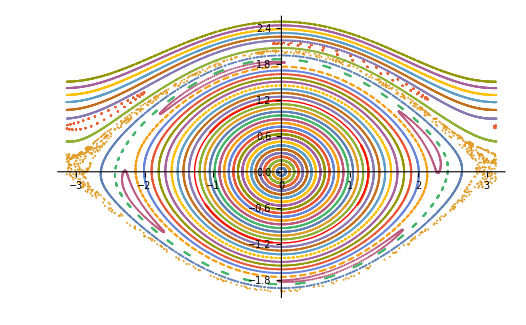

```mathematica
TripleResoPlot = ListPlot[Table[SnapSet[InitTable[[i]],1000,0.01,2.7],{i,1,imax}]]
Show[TripleResoPlot,ContourPlot[Energy[0.9]==1/2 p^2 - Cos[x],{x,-π,π},{p,-3,3},ContourStyle->Directive[Red,Thick]]]
```

The general pattern revealed by such experiments is that the system will often create these chains of stable and unstable periodic orbits with the corresponding “nonlinear pendulum”-like structures around them when the ratio of the frequencies is p:q with p,q integers.

## Why? The failure of near-identity “averaging” transforms

Consider the angles from AA variables τ,ψ. At a generic point their relative phase varies in time. Their evolution winds over the entire torus. At resonances, however, this is not the case, the combination of phases pτ-qψ has a zero time derivative at a p:q resonance between the frequencies. In that case, the torus “falls apart” into periodic orbits

One way to view this is as two oscillators.

```mathematica
Manipulate[ParametricPlot[{Sin[t+t0],Sin[ωrel t]},{t,0,100π}],{t0,0,2π},{{ωrel,1},0,10}]
```

One can then see that if the perturbation depends on the relative phase of the two angles, different relative phases will be perturbed by different persistent forces. 

Let us take a look at the pendulum perturbation in angle coordinates as we have computed it last time

```mathematica
ϵ Cos[2 JacobiAmplitude[2 ψ EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)],2/(1+En)]] Sin[τ]
<<FourierSeries`
NFourierSeries[ Cos[2 JacobiAmplitude[2 ψ EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)],2/(1+En)]]/.{En->0.},ψ,10]
```

ϵ Cos[2 JacobiAmplitude[2 ψ EllipticF[1/4 (π+2 ArcSin[En]),2/(1+En)],2/(1+En)]] Sin[τ]

0.477598-(0.021167-1.70071×10^-16 ⅈ) ⅇ^(-ⅈ ψ)-(0.021167+1.70071×10^-16 ⅈ) ⅇ^(ⅈ ψ)+0.0228856 ⅇ^(-2 ⅈ ψ)+0.0228856 ⅇ^(2 ⅈ ψ)-(0.0264947+1.29762×10^-17 ⅈ) ⅇ^(-3 ⅈ ψ)-(0.0264947-1.29762×10^-17 ⅈ) ⅇ^(3 ⅈ ψ)+0.0341076 ⅇ^(-4 ⅈ ψ)+0.0341076 ⅇ^(4 ⅈ ψ)-(0.0546416+6.18441×10^-17 ⅈ) ⅇ^(-5 ⅈ ψ)-(0.0546416-6.18441×10^-17 ⅈ) ⅇ^(5 ⅈ ψ)+0.223489 ⅇ^(-6 ⅈ ψ)+0.223489 ⅇ^(6 ⅈ ψ)+0.0795686 ⅇ^(-7 ⅈ ψ)+0.0795686 ⅇ^(7 ⅈ ψ)-(0.0296913+8.83487×10^-18 ⅈ) ⅇ^(-8 ⅈ ψ)-(0.0296913-8.83487×10^-18 ⅈ) ⅇ^(8 ⅈ ψ)+0.0163962 ⅇ^(-9 ⅈ ψ)+0.0163962 ⅇ^(9 ⅈ ψ)-(0.00983733+1.96576×10^-16 ⅈ) ⅇ^(-10 ⅈ ψ)-(0.00983733-1.96576×10^-16 ⅈ) ⅇ^(10 ⅈ ψ)

At a generic point, it has an infinite number of harmonics with respect to ψ. However, the magnitude of the coefficients asymptotically drops exponentially since the function is smooth, so only a couple of the first ones matter. (Do note that the sequence may not be strictly monotonous.) Multiplied by the Sin[τ] term, there is a “persistent” term in the Hamiltonian, e.g. ~ Cos[2ψ +τ] that depends on the relative “resonant” phase.

The chains on the Poincaré surfaces of sections correspond to differing relative phases between the pendulum oscillation and the driving. The resonant phase is constant only in the zeroth-order system, its true dynamics is dominated by the perturbation. The  ~ Cos[2ψ +τ] term then plays a role similar to the Cos[x] potential of the nonlinear pendulum. This is why we see a similar structure in the two problems.

## A more formal argument by computing perturbed action

From Arnolʹd, V. I., Kozlov, V. V., Neishtadt, A. I., & Iacob, I. (2006). Mathematical aspects of classical and celestial mechanics (Vol. 3, pp. XIII-505). Berlin: Springer.
These are excerpts from Chapter 6
-Graphics-

-Graphics-

where the curly bracket operator is the “oscillation integration operator”, and the averaging goes over the angle variables (over the torus). The oscillation integration operator is the formal solution of the following equation

-Graphics-

where there is implicit summation over all ψ^i and ω^i. One can express all of this by the Fourier series in action-angle variables:

The sum over k goes over all nonzero integer vector in N-dimensional space ℤ^N and the (,) is the Euclidean scalar product. (It is just a way to represent mode sums.)

The integration operator is obviously singular on a dense set. Is the perturbation valid at all??

This conundrum was answered by the Kolmogorov-Arnold-Moser theorem. It states that for smooth perturbations and up to an 𝒪(√ϵ) volume of phase space, the perturbation theory is valid and the tori survive the perturbation. Furthermore, they are well approximated by the perturbation theory above. 

How does the proof work? As already mentioned, smooth functions have an asymptotically exponential fall-off of the Fourier series in ψ^i. At every finite value of ϵ, we can split the perturbation into a part which has a finite number of Fourier coefficients and a part which has Fourier coefficients of relative size ϵ. These are classified as perturbations of higher order and one deals with perturbations with a finite number of singularities in the integration operator at each order. That is the main trick, the rest is proving that such a series converges up to a volume of order 𝒪(√ϵ) around resonances.